# Eikonal Representation of Wavefront and Polarization

Russell Chipman

University of Arizona & Airy Optics

```mathematica
Column[{"Draft",
DateString[Date[]],
NotebookFileName[]}]
```

Draft
Wed 3 Jul 2019 06:21:06
C:\Users\Russell\Documents\GitHub\WSS-Template\Final Project\Drafts\EikonalProject.RChipman.nb

Questions

Moving from Lists to Assignments
High dimensional geometrical representations

Project Objective

The objective is to develop Mathematica routines to extend the description of the performance of optical systems from a ray-based description to a polynomial description known as an eikonal, and to further to describe the polarization properties with polynomials which are the outer product of Zernike polynomials with Zernike polynomials.

## Polaris-M Polarization Ray Tracing Code

I .

## Example Optical System: Cooke Triplet

A simple optical system will be used for the development of these algorithms. The Cooke Triplet has three lenses and is effective in reducing the spherical aberration, coma, and astigmatism of the lens to acceptably low levels.

```mathematica
WikipediaData["Cooke Triplet"]
```

The Cooke triplet is a photographic lens designed and patented (patent number GB 22,607) in 1893 by Dennis Taylor who was employed as chief engineer by T. Cooke & Sons of York. It was the first lens system that allowed elimination of most of the optical distortion or aberration at the outer edge of lenses.


== Design ==

A Cooke triplet comprises a negative flint glass element in the centre with a crown glass element on each side. In this design, the sum of all the curvatures times indices of refraction can be zero, so that the field of focus is flat (zero Petzval field curvature). In other words, the negative lens can be as strong as the outer two combined, when one measures in dioptres, yet the lens will converge light, because the rays strike the middle element close to the optic axis. The curvature of field is determined by the sum of the dioptres, but the focal length is not. 
At the time, the Cooke triplet was a major advancement in lens design. It was superseded by later designs in high-end cameras, but is still widely used in inexpensive cameras, including variations using aspheric elements, particularly in cell-phone cameras.


== Application ==
The triplet soon became a standard in lens design still used with low-end cameras today. The main optical manufacturers often further developed the original Cooke triplet (e.g., the Zeiss Triotar) that were produced for many decades. 
Binoculars as well as refracting telescopes often use triplets. The same holds for many projection lenses, e.g., for 35 mm slide projectors.

		
		


== See also ==
Achromatic lens
Chromatic aberration

## Optical System Representation

#### Example Cooke Triplet Lens

#### Representation in Polaris-M

I .

```mathematica
os={{1,{"SPHERE",0.045425638230217134},"Air","Schott_N-BK7",{0,0,5},{0,0,1},{"Circle",10.,{0,0,5},{0,0,1}},{"Isotropic","Fresnel",{},{},{1,0,0},{},{},{},{0,0}},{"Refract"},{},""},{2,{"SPHERE",-0.002294841196989168},"Schott_N-BK7","Air",{0,0,8.259},{0,0,1},{"Circle",8.333333333333334,{0,0,8.259},{0,0,1}},{"Isotropic","Fresnel",{},{},{1,0,0},{},{},{},{0,0}},{"Refract"},{},""},{3,{"SPHERE",-0.045018682753342636},"Air","Schott_F2",{0,0,14.267},{0,0,1},{"Circle",6.666666666666666,{0,0,14.267},{0,0,1}},{"Isotropic","Fresnel",{},{},{1,0,0},{},{},{},{0,0}},{"Refract"},{},""},{4,{"SPHERE",0.04928050463236743},"Schott_F2","Air",{0,0,15.267},{0,0,1},{"Circle",6.666666666666666,{0,0,15.267},{0,0,1}},{"Isotropic","Fresnel",{},{},{1,0,0},{},{},{},{0,0}},{"Refract"},{},""},{5,{"SPHERE",0.01254957080467848},"Air","Schott_N-BK7",{0,0,20.017},{0,0,1},{"Circle",8.333333333333334,{0,0,20.017},{0,0,1}},{"Isotropic","Fresnel",{},{},{1,0,0},{},{},{},{0,0}},{"Refract"},{},""},{6,{"SPHERE",-0.07465472191116089},"Schott_N-BK7","Air",{0,0,22.969},{0,0,1},{"Circle",8.333333333333334,{0,0,22.969},{0,0,1}},{"Isotropic","Fresnel",{},{},{1,0,0},{},{},{},{0,0}},{"Refract"},{},""},{7,{"Plane"},"Air","Air",{0,0,28.336},{0,0,1},{"CIRCLE",10,{0,0,28.336},{0,0,1}},{"Isotropic","",{},{},{1.,0.,0.},{},{0.,0.},{},{}},{"Refract"},{},""},{8,{"SPHERE",0},"Air","Air",{0,0,68.336},{0,0,1},{"Circle",12,{0,0,68.336},{0,0,1}},{"Isotropic","Fresnel",{},{},{1,0,0},{},{},{},{0,0}},{"Refract"},{},""}};
```

```mathematica
PrintSystem[os]
```

#### Simplified Representation for Eikonal Project

To represent the continuous family of all Cooke triplet lenses near the “nominal” or “optimized” Cooke triplet lens, the lens representation is reduced to a single point in a 13-D space, the “Lens Space”, describing the curvatures and positions.

```mathematica
TableForm[
{{c1,"curvature of front surface, first element"},
{c2,"curvature of back surface, first element"}, 
{c3,"curvature of front surface, second element"},
{c4,"curvature of back surface, second element"}, 
{c5,"curvature of front surface, third element"},
{c6,"curvature of back surface, third element"}, 
{t1,"thickness of first element"},
{t2,"airspace from first to second element"}, 
{t3,"thickness of second element"},
{t4,"airspace from second to third element"}, 
{t5,"thickness of third element"},
{t6,"airspace from third element to exit pupil"},
{t7,"airspace from exit pupil to image plane"}}]
```

c1 | curvature of front surface, first element
c2 | curvature of back surface, first element
c3 | curvature of front surface, second element
c4 | curvature of back surface, second element
c5 | curvature of front surface, third element
c6 | curvature of back surface, third element
t1 | thickness of first element
t2 | airspace from first to second element
t3 | thickness of second element
t4 | airspace from second to third element
t5 | thickness of third element
t6 | airspace from third element to exit pupil
t7 | airspace from exit pupil to image plane

In this project, refractive indices and glass types will not be varies.

For a set of points, the lens will be analyzed for many optical properties. From the properties on this set of points, the goal is to reasonably approximate the properties of the lens family over a region of the space, i.e. to understand the properties of a large part of the family of lenses from the properties of a relatively small number of lenses.

```mathematica
field=4;
Show[PlotSystem[forwardRayTrace[[field]],opticalSystem,RayArrowStyle->{Black,Opacity[1],Arrowheads[.01]},Mesh->False,PlotStyle->{Green,Opacity[.25]}],PlotSystem[EPRays[[field]],EPSurf[[field]],Mesh->False,PlotStyle->{Blue,EdgeForm[{Blue,Thick}],Opacity[1]},RayArrowStyle->{Blue,Opacity[.5],Arrowheads[.01]}],PlotSystem[XPRays[[field]],XPSurf[[field]],Mesh->False,PlotStyle->{Red,EdgeForm[{Red,Thick}],Opacity[1]},RayArrowStyle->{Red,Opacity[.5],Arrowheads[.01]}],ImageSize->800,PlotRange->{{-12,12},{-12,12},{-10,40}}]
```

-Graphics3D-

#### curse of dimensionality

A practical limitation in lens design is the curse of dimensionality. As the number of dimensions Dim increases, the number of terms in a polynomial of order O increases as a Binomial function of Dim and O.

```mathematica
Column[Table[Binomial[n,k],{n,0,15},{k,0,n}],Center]
```

{1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}
{1,9,36,84,126,126,84,36,9,1}
{1,10,45,120,210,252,210,120,45,10,1}
{1,11,55,165,330,462,462,330,165,55,11,1}
{1,12,66,220,495,792,924,792,495,220,66,12,1}
{1,13,78,286,715,1287,1716,1716,1287,715,286,78,13,1}
{1,14,91,364,1001,2002,3003,3432,3003,2002,1001,364,91,14,1}
{1,15,105,455,1365,3003,5005,6435,6435,5005,3003,1365,455,105,15,1}

#### Aberrations

The image defects of a lens are its aberrations, deviations of the wavefronts from spherical. The aberrations of a radially symmetric system can be described by even order polynomials of two field coordinates {G,H} and two polar pupil coordinates {ρ,ϕ}. So lens aberrations are sorted into second order, fourth order, etc.

## Ray Representation

```mathematica
PlotSystem[raysout=TraceRays[Flatten[MeritFunctionRayset[{0,0,5},4,RayOrigin->"Infinite",Wavelengths->{.589},Fields->{{0,0,0},{0,1,0},{0,.7,0},{1,0,0},{.7,0,0},{1,1,0}/Sqrt[2],{.7,.7,0}/Sqrt[2],{0,-1,0},{0,-.7,0},{-1,0,0},{-.7,0,0},{-1,-1,0}/Sqrt[2],{-.7,-.7,0}/Sqrt[2],{-1,1,0}/Sqrt[2],{-.7,.7,0}/Sqrt[2],{1,-1,0}/Sqrt[2],{.7,-.7,0}/Sqrt[2]}],1],os],os]
```

-Graphics3D-

The calculation of a ray through an optical system can be considered as the fundamental calculation unit of analysis. To understand the aberrations, a sufficient number of lenses must be traced. A minimum number of rays across the pupil are needed, and a minimum number of fields must be traced from. The higher the order of the aberration, the more rays are needed to reveal the aberrations in the calculation.

## Lens Family

## Lens Bendings

```mathematica
GraphicsGrid[{Range[9],
tripletData[[All,1,1,2,-1,1]],
tripletData[[1,All,1,2,-1,2]],
tripletData[[1,1,All,2,-1,3]]},Spacings->{-5, 1},
Dividers->{False,{True,True,True,True,True}},ImageSize->600]
```

-Graphics-

## Etendue

## Eikonals

Eikonal function takes ray representation and places information in a polynomial representation.

```mathematica
EikonalFunctions[tr,{{1,ray`r,1},{1,ray`r,2},{1,ray`k,1},{1,ray`k,2}},{{-2,ray`OPLCumulative}},3]
```

{{OPLCumulativeSurf6},{26.8374+2.15658×10^9 k1Surf1-990.367 k1Surf1^2-2.1058×10^11 k1Surf1^3-7.3428×10^8 k2Surf1+0.0326266 k1Surf1 k2Surf1-2.50537×10^11 k1Surf1^2 k2Surf1-992.704 k2Surf1^2-2.1058×10^11 k1Surf1 k2Surf1^2+9.83559×10^9 k2Surf1^3+4.0965×10^7 r1Surf1-33.5474 k1Surf1 r1Surf1-1.21452×10^10 k1Surf1^2 r1Surf1-6.82563×10^8 k2Surf1 r1Surf1-7.09723×10^8 k1Surf1 k2Surf1 r1Surf1-6.69736×10^9 k2Surf1^2 r1Surf1-0.309472 r1Surf1^2-2.36975×10^8 k1Surf1 r1Surf1^2-3.63264×10^8 k2Surf1 r1Surf1^2-1.52109×10^6 r1Surf1^3-1.39479×10^7 r2Surf1+6.82563×10^8 k1Surf1 r2Surf1-1.38107×10^10 k1Surf1^2 r2Surf1-33.6377 k2Surf1 r2Surf1-5.44789×10^9 k1Surf1 k2Surf1 r2Surf1+5.50631×10^8 k2Surf1^2 r2Surf1+0.0000114687 r1Surf1 r2Surf1+8.39415×10^7 k1Surf1 r1Surf1 r2Surf1+4.60189×10^7 k2Surf1 r1Surf1 r2Surf1-1.79779×10^6 r1Surf1^2 r2Surf1-0.310344 r2Surf1^2-2.82994×10^8 k1Surf1 r2Surf1^2+1.14511×10^7 k2Surf1 r2Surf1^2-1.52109×10^6 r1Surf1 r2Surf1^2+72168.6 r2Surf1^3},{6.84501×10^-7}}

### Exploring the Triplet Lens Parameter Space

```mathematica
triplet[3,1,9]
triplet[1,1,1]
```

Trace small number of the triplets for algorithm development
1.	Describe each triplet by lens indices over 9 lenses on slot machine triplet[3,1,9]				7/2
	a.		Nine first elements {1,2, …,9}
	b.		Nine second elements {1,2, …,9}
	c.		Nine third elements {1,2, …,9}
2.	Create ray sets for entrance pupil, use same ray set for all lenses 							7/2
	a.		Each have same entrance pupil with respect to first surface
3.	Trace rays from planar surface before lens perpendicular to rays to spherical surface centered on real chief ray intersection on image plane passing through center of exit pupil
	a.		Relative field heights of 0, 0.6, 0.9, 1.0
4.	Calculate Zernike polynomials through 36th order for each of four fields						7/3
5.	Save into data structure																7/3
	a.		calculateTriplet[lens1,lens2,lens3]:={
	b.		{lens1,lens2,lens3},{c1,c2,c3…c6,z1,z2,…z8},{exit pupil diameter},
	c.		{f1 Zernike polynomials, f2 Zernike polynomials, f3 Zernike polynomials, f4 Zernike polynomials,},
	d.		{z for plane of best overall focus},
	e.		”ray file name” }
	f.		May be other fields important or necessary to add
6.	To collect information across lenses for fitting Zernike coefficients in {c1,c2,c3…c6,z1,z2,…z8} space use	7/4
	a.		Downvalues[calculateTriplet] 
7. 	Calculate Zernike coefficients for a set of 9^3 lenses												7/6
	a.		Several day background calculation.
8.	Fitting Zernike coefficients to lens constructional parameters, ,{c1,c2,c3…c6,z1,z2,…z8}
9.	Performing calculations over the lens family
	a.		RMS spot size
	b.		Average wavefront aberration

## Comments on Zernike Polynomials

Zernike polynomials are a set of basis functions for real scalar functions defined on a circle. Zernike polynomials are widely used for the representation of wavefront aberration. For a specified object point, the optical path length to a spherical surface in the exit pupil is OPL[x_p,y_p] is fit to the set of Zernike polynomials, each basis function receiving a coefficient for each term {Z_1,Z_2,Z_3,…,Z_max}. The number of terms,  Z_max, is chosen to reach a given level of accuracy in the representation. For the triplet lens family, max=36 provides sufficient accuracy.

A single wavefront from a single object point is described by a set of Zernike polynomials.

### Zernike polynomial aberration names

```mathematica
zernikeNames={{"Piston"}, {"X-Tilt"}, {"Y-Tilt"}, {"Defocus"}, {"Oblique Astigmatism"}, {"Vertical Astigmatism"}, {"Vertical Coma"}, {"Horizontal Coma"}, {"Vertical Trefoil"}, {"Oblique Trefoil"}, {"Spherical"}, {"Vertical Secondary Astigmatism"}, {"Oblique Secondary Astigmatism"}, {"Vertical Quadrafoil"}, {"Oblique Quadrafoil"}}//Flatten;zernikeNames//FullForm
```

```mathematica
zernikeNames=List["Piston","X-Tilt","Y-Tilt","Defocus","Oblique Astigmatism","Vertical Astigmatism","Vertical Coma","Horizontal Coma","Vertical Trefoil","Oblique Trefoil","Spherical","Vertical Secondary Astigmatism","Oblique Secondary Astigmatism","Vertical Quadrafoil","Oblique Quadrafoil"];
```

#### Example of Zernike variation over field of view

```mathematica
fourFieldZernike={{{104830.16883976161,0,0,-1.0353221896434401,0,0,0,0,0,0,-0.3495406804372394,0,0,-0.0009583841126657343,0},{104827.42819554721,0,4.21644531682368,-3.6281202606695495,0,2.706220015267057,0.09284801235041129,0,-0.0457036515332004,0,-0.4258313874447901,0.05901109599597848,0,-0.002900171313865151,0},{104823.05394474449,0,8.060450522707786,-7.041658114736383,-4.5002829828922523*^-10,6.39661505432036,0.3415984471753944,-5.787977587184015*^-10,-0.16018177347512855,-6.7389331435825*^-10,-0.5111695449521755,0.15032315258227258,6.244409129463521*^-10,-0.01025519684576501,-3.2028513736905*^-10},{104820.88325932846,0,9.810173638523377,-8.551639605976293,0,8.049793343431547,0.48400937781439585,0,-0.22692281271770795,0,-0.5503744620604288,0.19504946016374866,0,-0.015416379344407035,0}},{0.,0.,12.724888892019564},6.25605586092761,{0.,0.,10.620314285844316},6.330385750953205}[[1]];
```

```mathematica
TableForm[Transpose[fourFieldZernike],TableHeadings->{zernikeNames,{1,2,3,4}}]
```

| 1 | 2 | 3 | 4
Piston | 104830. | 104827. | 104823. | 104821.
X-Tilt | 0 | 0 | 0 | 0
Y-Tilt | 0 | 4.21645 | 8.06045 | 9.81017
Defocus | -1.03532 | -3.62812 | -7.04166 | -8.55164
Oblique Astigmatism | 0 | 0 | -4.50028×10^-10 | 0
Vertical Astigmatism | 0 | 2.70622 | 6.39662 | 8.04979
Vertical Coma | 0 | 0.092848 | 0.341598 | 0.484009
Horizontal Coma | 0 | 0 | -5.78798×10^-10 | 0
Vertical Trefoil | 0 | -0.0457037 | -0.160182 | -0.226923
Oblique Trefoil | 0 | 0 | -6.73893×10^-10 | 0
Spherical | -0.349541 | -0.425831 | -0.51117 | -0.550374
Vertical Secondary Astigmatism | 0 | 0.0590111 | 0.150323 | 0.195049
Oblique Secondary Astigmatism | 0 | 0 | 6.24441×10^-10 | 0
Vertical Quadrafoil | -0.000958384 | -0.00290017 | -0.0102552 | -0.0154164
Oblique Quadrafoil | 0 | 0 | -3.20285×10^-10 | 0

### Zernikes at four fields, 0, 0.6, 0.9, 1 of full field height

```mathematica
(* Display zernikes for all fields *)
PrintZernike[#]&/@zernikes
```

{Noll | Z(n,m) | Value | Name
1 | Z_0^0 | -0.00959537 | Piston
2 | Z_1^1 | 0 | X-Tilt
3 | Z_1^-1 | 0 | Y-Tilt
4 | Z_2^0 | 0.131468 | Defocus
5 | Z_2^-2 | 0 | Oblique Astigmatism
6 | Z_2^2 | 0 | Vertical Astigmatism
7 | Z_3^-1 | 0 | Vertical Coma
8 | Z_3^1 | 0 | Horizontal Coma
9 | Z_3^-3 | 0 | Vertical Trefoil
10 | Z_3^3 | 0 | Oblique Trefoil
11 | Z_4^0 | 0.0480674 | Spherical
12 | Z_4^-2 | 0 | Vertical Secondary Astigmatism
13 | Z_4^2 | 0 | Oblique Secondary Astigmatism
14 | Z_4^4 | 0.00109703 | Vertical Quadrafoil
15 | Z_4^-4 | 0 | Oblique Quadrafoil,Noll | Z(n,m) | Value | Name
1 | Z_0^0 | -0.0167075 | Piston
2 | Z_1^1 | 0 | X-Tilt
3 | Z_1^-1 | -0.30659 | Y-Tilt
4 | Z_2^0 | 0.363466 | Defocus
5 | Z_2^-2 | 0 | Oblique Astigmatism
6 | Z_2^2 | -0.0822932 | Vertical Astigmatism
7 | Z_3^-1 | 0.312114 | Vertical Coma
8 | Z_3^1 | 0 | Horizontal Coma
9 | Z_3^-3 | -0.00356279 | Vertical Trefoil
10 | Z_3^3 | 0 | Oblique Trefoil
11 | Z_4^0 | 0.051592 | Spherical
12 | Z_4^-2 | -0.00311584 | Vertical Secondary Astigmatism
13 | Z_4^2 | 0 | Oblique Secondary Astigmatism
14 | Z_4^4 | 0.00113121 | Vertical Quadrafoil
15 | Z_4^-4 | 0 | Oblique Quadrafoil,Noll | Z(n,m) | Value | Name
1 | Z_0^0 | -0.0206059 | Piston
2 | Z_1^1 | 0 | X-Tilt
3 | Z_1^-1 | 0.252232 | Y-Tilt
4 | Z_2^0 | 0.654902 | Defocus
5 | Z_2^-2 | 0 | Oblique Astigmatism
6 | Z_2^2 | -0.182671 | Vertical Astigmatism
7 | Z_3^-1 | 0.474727 | Vertical Coma
8 | Z_3^1 | 0 | Horizontal Coma
9 | Z_3^-3 | -0.0103304 | Vertical Trefoil
10 | Z_3^3 | 0 | Oblique Trefoil
11 | Z_4^0 | 0.0561533 | Spherical
12 | Z_4^-2 | -0.00721667 | Vertical Secondary Astigmatism
13 | Z_4^2 | 0 | Oblique Secondary Astigmatism
14 | Z_4^4 | 0.00121034 | Vertical Quadrafoil
15 | Z_4^-4 | 0 | Oblique Quadrafoil,Noll | Z(n,m) | Value | Name
1 | Z_0^0 | -0.0205906 | Piston
2 | Z_1^1 | 0 | X-Tilt
3 | Z_1^-1 | 0.621585 | Y-Tilt
4 | Z_2^0 | 0.778328 | Defocus
5 | Z_2^-2 | 0 | Oblique Astigmatism
6 | Z_2^2 | -0.223996 | Vertical Astigmatism
7 | Z_3^-1 | 0.530761 | Vertical Coma
8 | Z_3^1 | 0 | Horizontal Coma
9 | Z_3^-3 | -0.0139528 | Vertical Trefoil
10 | Z_3^3 | 0 | Oblique Trefoil
11 | Z_4^0 | 0.0581301 | Spherical
12 | Z_4^-2 | -0.00901495 | Vertical Secondary Astigmatism
13 | Z_4^2 | 0 | Oblique Secondary Astigmatism
14 | Z_4^4 | 0.00125444 | Vertical Quadrafoil
15 | Z_4^-4 | 0 | Oblique Quadrafoil}

#### Zernike’s for fitting over FOV

```mathematica
zList=Transpose[fourFieldZernike[[All,{3,4,6,7,9,11,12,14}]]]
```

{{0,4.21645,8.06045,9.81017},{-1.03532,-3.62812,-7.04166,-8.55164},{0,2.70622,6.39662,8.04979},{0,0.092848,0.341598,0.484009},{0,-0.0457037,-0.160182,-0.226923},{-0.349541,-0.425831,-0.51117,-0.550374},{0,0.0590111,0.150323,0.195049},{-0.000958384,-0.00290017,-0.0102552,-0.0154164}}

#### Corresponding fields of view

```mathematica
fields={0,.6,.9,1.};
Transpose[{fields,zList[[1]]}]
```

{{0,0},{0.6,4.21645},{0.9,8.06045},{1.,9.81017}}

#### Match Zernike coefficients with Fields for fitting

```mathematica
zFields=Transpose[{fields,#}] & /@ zList
```

{{{0,0},{0.6,4.21645},{0.9,8.06045},{1.,9.81017}},{{0,-1.03532},{0.6,-3.62812},{0.9,-7.04166},{1.,-8.55164}},{{0,0},{0.6,2.70622},{0.9,6.39662},{1.,8.04979}},{{0,0},{0.6,0.092848},{0.9,0.341598},{1.,0.484009}},{{0,0},{0.6,-0.0457037},{0.9,-0.160182},{1.,-0.226923}},{{0,-0.349541},{0.6,-0.425831},{0.9,-0.51117},{1.,-0.550374}},{{0,0},{0.6,0.0590111},{0.9,0.150323},{1.,0.195049}},{{0,-0.000958384},{0.6,-0.00290017},{0.9,-0.0102552},{1.,-0.0154164}}}

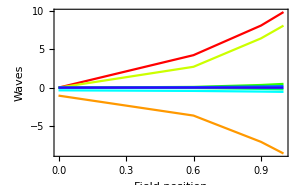
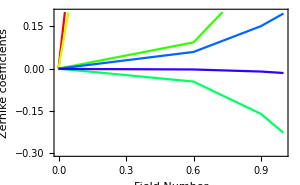

```mathematica
Row[{ListPlot[zFields,Joined->True,PlotStyle->Table[Hue[e],{e,0,1,.1}],PlotRange->All,Frame->True, FrameLabel->{"Field position","Waves","Zernike coefficients"},ImageSize->300],ListPlot[zFields,Joined->True,PlotStyle->Table[Hue[e],{e,0,1,.1}],PlotRange->{{0,1},{-.3,.2}},Frame->True, FrameLabel->{"Field Number","Zernike coefficients"},ImageSize->300]}]
```

#### Zernike symmetries

```mathematica
{{, "Symmetry", "Angular Symmetry", Subscript[ϕ, 0], "Index"}, {"Piston", "Even", 0, □, 1}, {"X-Tilt", "Zero", 1, π/2, 2}, {"Y-Tilt", "Odd", 1, 0, 3}, {"Defocus", "Even", 0, □, 4}, {"Oblique Astigmatism", "Zero", 2, π/2, 5}, {"Vertical Astigmatism", "Even", 2, 0, 6}, {"Vertical Coma", "Odd", 1, 0, 7}, {"Horizontal Coma", "Zero", 1, π/2, 8}, {"Vertical Trefoil", "Even", 3, 0, 9}, {"Oblique Trefoil", "Zero", 3, π/3, 10}, {"Spherical", "Even", 0, □, 11}, {"Vertical Secondary Astigmatism", "Even", 2, 0, 12}, {"Oblique Secondary Astigmatism", "Zero", 2, π/2, 13}, {"Vertical Quadrafoil", "Even", 4, 0, 14}, {"Oblique Quadrafoil", "Zero", 4, π/8, 15}}
```

#### Terms for fitting

```mathematica
evenZ={1,4,6,9,11,12,14};
oddZ={3,7};
```

## ZernZernike functions

Each object point has a different set of Zernike coefficients. So each Zernike coefficient for a lens varies as a function of object coordinates {x_0,y_0}. So for the lens with a circular object, the variation of each Zernike coefficient with {x_0,y_0} can be a written as another Zernike polynomial. Thus the description of the wavefront over all object points is expressed as the outer product of Zernike polynomials with Zernike polynomials.

#### Fields where Zernike coefficients were calculated

```mathematica
fields={0,.6,.9,1};
```

#### Even and Odd polynomial fits

```mathematica
Clear[zn,evenPoly,oddPoly]
```

```mathematica
evenPoly[l_,m_,n_,zn_]:=Fit[Transpose[{fields,Transpose[data[[l,m,n,2,3]]][[zn]]}],{1,x^2,x^4,x^6},x]
oddPoly[l_,m_,n_,zn_]:=Fit[Transpose[{fields,Transpose[data[[l,m,n,2,3]]][[zn]]}],{0,x,x^3,x^5},x]
```

Example polynomials for lens 5,5,5

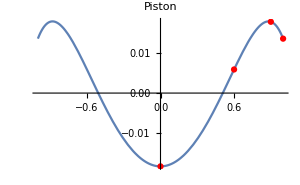
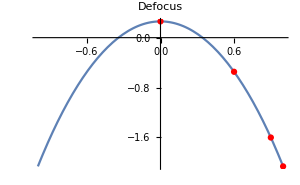
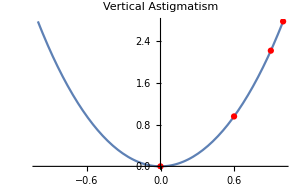
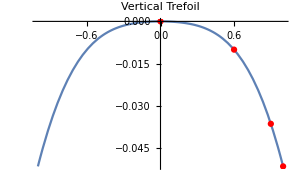
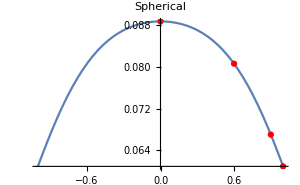
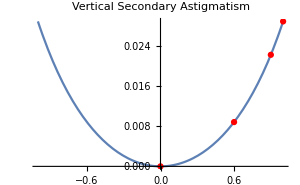
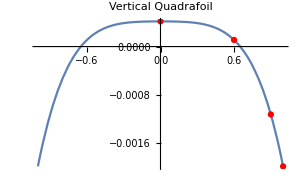

```mathematica
Show[Plot[Evaluate[evenPoly[5,5,5,#]],{x,-1,1},ImageSize->300],ListPlot[Transpose[{fields,Transpose[data[[5,5,5,2,3]]][[#]]}],PlotStyle->{PointSize[.015],Red}],PlotLabel->zernikeNames[[#]]]& /@  evenZ
```

#### Set order of polynomials

```mathematica
polyOrder=7;
```

#### Get Polynomial coefficients for example 1,1,1

```mathematica
AbsoluteTiming[zernFieldPoly={
PadRight[CoefficientList[evenPoly[1,1,1,1],x],polyOrder],
{0,0,0,0,0,0,0},
PadRight[CoefficientList[oddPoly[1,1,1,3],x],polyOrder],
PadRight[CoefficientList[evenPoly[1,1,1,4],x],polyOrder],
{0,0,0,0,0,0,0},
PadRight[CoefficientList[evenPoly[1,1,1,6],x],polyOrder],
PadRight[CoefficientList[oddPoly[1,1,1,7],x],polyOrder],
{0,0,0,0,0,0,0},
PadRight[CoefficientList[evenPoly[1,1,1,9],x],polyOrder],
{0,0,0,0,0,0,0},
PadRight[CoefficientList[evenPoly[1,1,1,11],x],polyOrder],
PadRight[CoefficientList[evenPoly[1,1,1,12],x],polyOrder],
{0,0,0,0,0,0,0},
PadRight[CoefficientList[evenPoly[1,1,1,14],x],polyOrder],
{0,0,0,0,0,0,0}}];
Map[Flatten,Transpose[{Range[15],ConstantArray["   ",15],zernFieldPoly,zernikeNames}]]//TableForm
```

1 |     | -0.295813 | 0 | -0.374918 | 0 | -2.14588 | 0 | -0.308728 | Piston
2 |     | 0 | 0 | 0 | 0 | 0 | 0 | 0 | X-Tilt
3 |     | 0. | -39.6589 | 0 | 11.6271 | 0 | 0.582875 | 0 | Y-Tilt
4 |     | 2.07967 | 0 | -8.64479 | 0 | -2.03961 | 0 | 0.549494 | Defocus
5 |     | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Oblique Astigmatism
6 |     | -1.19395×10^-15 | 0 | 8.3042 | 0 | 4.1571 | 0 | -0.725276 | Vertical Astigmatism
7 |     | 0. | 30.2891 | 0 | 6.47275 | 0 | 0.0664694 | 0 | Vertical Coma
8 |     | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Horizontal Coma
9 |     | 7.24901×10^-16 | 0 | -2.6703 | 0 | -2.31999 | 0 | 0.3241 | Vertical Trefoil
10 |     | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Oblique Trefoil
11 |     | 0.631546 | 0 | -0.492281 | 0 | -0.939709 | 0 | 0.516814 | Spherical
12 |     | -2.66508×10^-16 | 0 | -0.222912 | 0 | 1.6654 | 0 | -0.920563 | Vertical Secondary Astigmatism
13 |     | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Oblique Secondary Astigmatism
14 |     | -0.0350447 | 0 | 0.227885 | 0 | -1.0207 | 0 | 0.660142 | Vertical Quadrafoil
15 |     | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Oblique Quadrafoil

## Space of Cooke Triplet lenses and Its aberrations

The lens prescription space has been sampled and ZernZernikes calculated for nearly a thousand lenses. 
For each of the three lens elements, nine lenses have been selected. These are the nine lens elements, Lens1[1], … Lens1[9], chosen for the first lens. The lens has been “bended” so that the focal length of all nine lenses is equal by changing the two lens curvatures.

These are the nine lens elements, Lens2[1], … Lens2[9], chosen for the second lens.

These are the nine lens elements, Lens3[1], … Lens3[9], chosen for the second lens.

Taking all the combinations of the elements provides a set of

```mathematica
9^3
```

729

distinct lenses: triplet[1,1,1], triplet[1,1,2], …, triplet[9,9,9].

The ZernZernike coefficients have been evaluated for the full set of rays providing a complete information on the wavefront aberrations for the entire lens and field of view.

### Part of Lens Design Space with Best Image Quality

The region around the lens triplet[5,5,5] is near the region of optimal lens performance using a metric of the RMS value of the ZernZernike coefficients,
aberrationRMS= √(∑_(i,j=1)^36 ZZ_(i,j)).

## Fitting the ZernZernike Polynomials vs the lens constructional parameters

Given a ZernZernike description of each Cooke triplet, {ZZ_(1,1),…,ZZ_(36,36)} these coefficients can be fit to low order polynomials in the lens constructional parameters, {c_1,c_2,c_3,c_4,c_5,c_6,t_1,t_2,t_3,t_4,t_5,t_6,t_7}. Each constructional parameter varies over a range Min[c_1]≤c_1≤Max[c_1].
So each of the ZernZernike coefficients will be fit to a low order polynomial, linear, quadratic, cubic in combinations of the c’s and t’s. 
Finding variation of each Zernike polynomial coefficient versus the constructional parameters.

#### Symmetries of the Zernike coefficients with field

## Further explorations

## Questions

Encode[ ]

Assignments

## Notes

## Acknowledgements

Alex Erstad and Brian Daugherty collaborated in the development of these algorithms..

## Author contact information

rchipman@optics.arizona.edu

## Functions

### Options

```mathematica
Options[CreateEmissionsStokesImage]=Join[{

figResolution->10,(*for output sampling, gives output tables around 40x50*)
imageResolution->100(*number of points in calcultion, 100 is smooth but slow*),
xyzDigits->4,
DoLPDigits->4,
S012Digits->3,
saveData->False(*Enter FileName within quotes if you want files saved*)
},
{}
];
Options[CreateEmissionsStokesImage]//TableForm
```

figResolution→10
imageResolution→100
xyzDigits→4
DoLPDigits→4
S012Digits→3
saveData→False

### Functions

### Main function

## Notes to self

# Extra code

#### Zernike from Mathematica documentation

```mathematica
r2c[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>x/r}/.r^n_:>(x^2+y^2)^(n/2)]
```

```mathematica
zPlot[e_]:=With[{f= r2c[e]},DensityPlot[Cos[2 Pi f]^2,{x,-1,1},{y,-1,1},RegionFunction:>(#1^2+#2^2≤1&),PlotPoints->50,BoundaryStyle->Black,Frame->False]]
```

Visualize the combined effect of x-astigmatism and y-coma aberrations:

```mathematica
zPlot[ZernikeR[2,2,r]Cos[2θ]+2ZernikeR[3,1,r]Sin[θ]]
```

-Graphics-

Why didn’t plot3D work?

```mathematica
z3Plot[e_]:=With[{f= r2c[e]},Plot3D[Cos[2 Pi f]^2,{x,-1,1},{y,-1,1},RegionFunction:>(#1^2+#2^2≤1&),PlotPoints->50,BoundaryStyle->Black]]
```

```mathematica
z3Plot[ZernikeR[2,2,r]Cos[2θ]+2ZernikeR[3,1,r]Sin[θ],PlotRange->All]
```

z3Plot[{0.547023 r^2+0.951817 r (-2+3 r^2),0.957133 r^2-0.292805 r (-2+3 r^2),-0.729408 r^2+1.85979 r (-2+3 r^2)},PlotRange→All]

#### Data structure tabulatedShort

```mathematica
dataFields={
"zernikes",
"opsys0",
"entPupSurf",
"backTraceSys",
"forwardTrace",
"toEntPup",
"raysOutXP",
"{enPup,enPupRad*2}",
"{exitPup,exPupRad*2}",
"opsys0[[1;;-2,sys`shape`curv]]",
"opsys0[[1;;-2,sys`v]]",
"Lens indices,{lens1,lens2,lens3}",
"shapesCurvTab"
};
```

```mathematica
TableForm[Transpose[{Range[6],dataFields[[{12,10,11,8,9,1}]]}]]
```

1 | Lens indices,{lens1,lens2,lens3}
2 | opsys0[[1;;-2,sys`shape`curv]]
3 | opsys0[[1;;-2,sys`v]]
4 | {enPup,enPupRad*2}
5 | {exitPup,exPupRad*2}
6 | zernikes

### Aberration behavior

#### Defocus

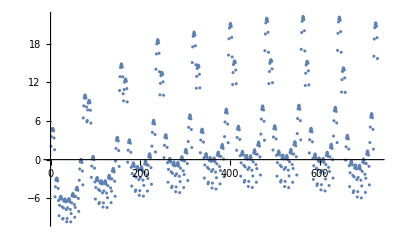

```mathematica
ListPlot[Flatten[tripletData[[All,All,All,2,1,1,4]]]]
```

```mathematica
{Max[#],Min[#]}&/@tripletData[[All,All,All,2,1,1,11]]
```

{{3.43971,-3.43293},{5.07787,-2.45195},{6.2794,-1.85227},{6.64697,-1.68247},{7.06116,-1.51227},{7.31322,-1.44267},{7.39977,-1.44759},{7.39341,-1.60379},{7.1547,-1.93056}}

#### Spherical ab

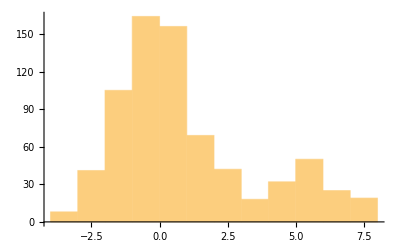

```mathematica
Histogram[Flatten[tripletData[[All,All,All,2,1,1,11]]]]
```

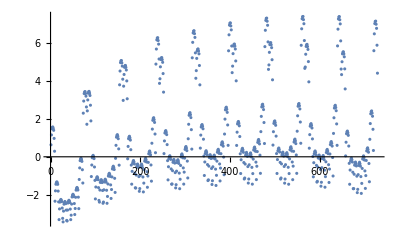

```mathematica
ListPlot[Flatten[tripletData[[All,All,All,2,1,1,11]]]]
```

#### Coma

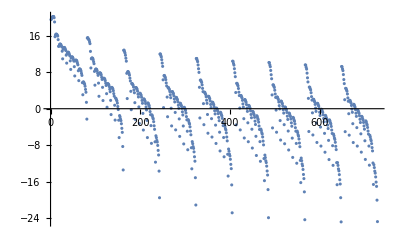

```mathematica
ListPlot[Flatten[tripletData[[All,All,All,2,1,2,7]]]]
```

#### Astigmatism

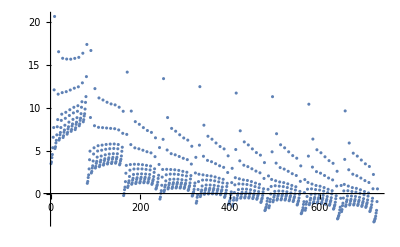

```mathematica
ListPlot[Flatten[tripletData[[All,All,All,2,1,2,6]]]]
```

### Rendering in the lens index space

```mathematica
point=20;
Graphics3D[{Table[{PointSize[.05*rmsData[[aa,3]]],Hue[rmsData[[aa,1]]],Point[combinations[[aa]]]},{aa,1,Length[combinations]}]},Axes->True,AxesLabel->{Style["Lens 1",point],Style["Lens 2",point],Style["Lens 3",point]}]
```

-Graphics3D-